## Fisher Information matrices for functional response models

```mathematica
Clear["Global`*"]
(* SetDirectory[NotebookDirectory[]] *)
```

The Fisher information matrix is the Hessian of the negative log-likelihood or, equivalently, the negative Hessian of the log-likelihood.
The Observed Fisher information matrix is the Fisher information matrix evaluated at the MLE.
The Expected Fisher information matrix is the Fisher information matrix “of sample size 1” (Myung et al. 2006, below eqn. 10), i.e. the expectation of the Fisher matrix evaluated over the probability distribution of x_i samples (e.g., x_i \[Distributed] Poisson).  We also take the expectation over the (experiment’s) variables, which in the context of functional responses is Ν and P (and, in the general sense, time T, which we do not do here).
Structural complexity is the natural log of the integration (over all parameters) of the square root of the determinant of the Expected Fisher Information matrix (Myung et al. 2006, 3rd part of RHS of eqn. 10)

### Define functions to compute hessian and fisher matrix of a function given the vector of its parameters

```mathematica
hessian[fun_,pars_]:= D[Apply[fun,pars],{pars,2}]
fisher[fun_,pars_]:=- hessian[fun,pars]
```

#### Test case

```mathematica
f[x_,y_]:=(x^2-y)/(x^2+y^2+1);
hessian[f,{x,y}]//MatrixForm
fisher[f,{x,y}]//FullSimplify//MatrixForm
```

((8 x^2 (x^2-y))/((1+x^2+y^2)^3)-(8 x^2)/((1+x^2+y^2)^2)-(2 (x^2-y))/((1+x^2+y^2)^2)+2/(1+x^2+y^2) | (8 x (x^2-y) y)/((1+x^2+y^2)^3)+(2 x)/((1+x^2+y^2)^2)-(4 x y)/((1+x^2+y^2)^2)
(8 x (x^2-y) y)/((1+x^2+y^2)^3)+(2 x)/((1+x^2+y^2)^2)-(4 x y)/((1+x^2+y^2)^2) | (8 (x^2-y) y^2)/((1+x^2+y^2)^3)-(2 (x^2-y))/((1+x^2+y^2)^2)+(4 y)/((1+x^2+y^2)^2))

((2 (-1+3 x^2-y^2) (1+y+y^2))/((1+x^2+y^2)^3) | -(2 x (1+x^2 (1+2 y)-y (2+y (3+2 y))))/((1+x^2+y^2)^3)
-(2 x (1+x^2 (1+2 y)-y (2+y (3+2 y))))/((1+x^2+y^2)^3) | (2 (x^4-3 y+y^3+x^2 (1-3 y (1+y))))/((1+x^2+y^2)^3))

### Define Functional responses - Number prey eaten

```mathematica
H1 = a Ν P T;
H2 = (a Ν P T)/(1+a h Ν);
BD = (a Ν P T)/(1+a h Ν + γ P);
CM = (a Ν P T)/((1+a h Ν)(1+γ P));
R = (a Ν P T)/P;
HV = (a Ν P T)/P^m;
AG = (a Ν P T)/(P+a h Ν);
AA=(a Ν P T)/(P^m+a h Ν);
```

### Probability density

```mathematica
PoissPDF=PDF[PoissonDistribution[λ],x][[1,1,1]]
```

(ⅇ^-λ λ^x)/(x!)

```mathematica
PoissPDFH1=PoissPDF/.{λ-> H1}
```

(ⅇ^(-a P T Ν) (a P T Ν)^x)/(x!)

### Experimental Designs

#### Option 1 - Discrete treatments

```mathematica
Νvals={5,20};
Pvals={1,2};
(* 
Νvals={1,2,4,8,10,15,20}; 
Pvals={1,2,4};
*)
Νprobs=ConstantArray[1/Length[Νvals],Length[Νvals]];
Pprobs=ConstantArray[1/Length[Pvals],Length[Pvals]];
ΝDistE=EmpiricalDistribution[Νprobs->Νvals];
PDistE=EmpiricalDistribution[Pprobs->Pvals];
```

#### Option 2 - Continuous treatments

```mathematica
ΝDist=UniformDistribution[{5,20}];
PDist=UniformDistribution[{1,2}];
```

### Define Expectation Function

AbsoluteTiming[] shows that use of Expectation[] is faster than Integrating over PDF.
AbsoluteTiming[] indicates that it is faster to compute expectations over Ν and P sequentially than to do so simultaneously.
AbsoluteTiming[] also indicates that it is faster to compute expectations over  P before N (but that might be a function of the number or range of N levels versus P levels in the experimental design).

```mathematica
EFisher[Fisher_,func_]:=
Expectation[
Expectation[
Expectation[
Fisher,
x\[Distributed] PoissonDistribution[func]],
P\[Distributed]PDistE], (* Replace option here *)
Ν\[Distributed]ΝDistE] (* Replace option here *)
```

## Fisher information matrices and determinants

#### Likelihood and substitutions

Note: If x_i\[Distributed]Poission(λ_i) for i = 1,...,n are independent and λ = ∑ λ_i, then Y=∑λ_i\[Distributed]Poission(λ).     Therefore we can just replace ∑_(i=1)^n x_i→ x.  
(See https://en.wikipedia.org/wiki/Poisson_distribution#Properties)

```mathematica
subsA={∑_(i=1)^n Subscript[x, i]-> x};
```

See MLE.bias for derivation of logLikelihood.

```mathematica
PoislL[func_]:=-n func-Log[∏_(i=1)^n Subscript[x, i]!]+Log[func] ∑_(i=1)^n Subscript[x, i]/.subsA
```

```mathematica
subsB={n-> 1,T-> 1};
```

AbsoluteTiming also indicates that performing subB substituting for each part within EFisher speeds things up.

#### Holling Type I model - Poisson

```mathematica
lLH1Poiss[a_]:=PoislL[H1]
FisherH1Poiss=fisher[lLH1Poiss,{a}];
%//FullSimplify//MatrixForm
```

(x/a^2)

```mathematica
EFisherH1Poiss=EFisher[FisherH1Poiss/.subsB,H1/.subsB];
%//MatrixForm
```

(75/(4 a))

```mathematica
DetH1=Det[EFisherH1Poiss]
```

75/(4 a)

#### Holling Type II model - Poisson

```mathematica
lLH2Poiss[a_,h_]:=PoislL[H2]
FisherH2Poiss=fisher[lLH2Poiss,{a, h}];
%//FullSimplify//MatrixForm
```

((x+3 a h x Ν+2 a^2 h (-n P T+h x) Ν^2)/(a^2 (1+a h Ν)^3) | (Ν (x-2 a n P T Ν+a h x Ν))/(1+a h Ν)^3
(Ν (x-2 a n P T Ν+a h x Ν))/(1+a h Ν)^3 | -(a^2 Ν^2 (x-2 a n P T Ν+a h x Ν))/(1+a h Ν)^3)

```mathematica
EFisherH2Poiss=EFisher[FisherH2Poiss/.subsB,H2/.subsB];
%//FullSimplify//MatrixForm
```

((75 (1+8 a h))/(4 a (1+5 a h)^2 (1+20 a h)^2) | ((15 a h (2+25 a h (3+16 a h)))/((1+5 a h)^2 (1+20 a h)^2)+2 Log[1+5 a h]-2 Log[1+20 a h])/(20 a^2 h^3)
((15 a h (2+25 a h (3+16 a h)))/((1+5 a h)^2 (1+20 a h)^2)+2 Log[1+5 a h]-2 Log[1+20 a h])/(20 a^2 h^3) | (3 ((5 h (6+25 a h (9+10 a h (9+40 a h (1+2 a h)))))/((1+5 a h)^2 (1+20 a h)^2)+(2 (Log[1+5 a h]-Log[1+20 a h]))/a))/(20 h^4))

```mathematica
DetH2=Det[EFisherH2Poiss]//FullSimplify
```

(225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))/(200 a^4 h^6 (1+5 a h)^2 (1+20 a h)^2)

#### Beddington-DeAngelis model - Poisson

```mathematica
lLBDPoiss[a_,h_,γ_]:=PoislL[BD]
FisherBDPoiss=fisher[lLBDPoiss,{a, h,γ}]//FullSimplify;
%//MatrixForm
```

(((1+P γ) (-2 a^2 h n P T Ν^2+x (1+P γ+a h Ν) (1+P γ+2 a h Ν)))/(a^2 (1+P γ+a h Ν)^3) | ((1+P γ) Ν (x+P x γ-2 a n P T Ν+a h x Ν))/(1+P γ+a h Ν)^3 | -(P Ν (n P T (1+P γ-a h Ν)+h x (1+P γ+a h Ν)))/(1+P γ+a h Ν)^3
((1+P γ) Ν (x+P x γ-2 a n P T Ν+a h x Ν))/(1+P γ+a h Ν)^3 | -(a^2 Ν^2 (x+P x γ-2 a n P T Ν+a h x Ν))/(1+P γ+a h Ν)^3 | (a P Ν (2 a n P T Ν-x (1+P γ+a h Ν)))/(1+P γ+a h Ν)^3
-(P Ν (n P T (1+P γ-a h Ν)+h x (1+P γ+a h Ν)))/(1+P γ+a h Ν)^3 | (a P Ν (2 a n P T Ν-x (1+P γ+a h Ν)))/(1+P γ+a h Ν)^3 | -(P^2 (x+P x γ-2 a n P T Ν+a h x Ν))/(1+P γ+a h Ν)^3)

```mathematica
EFisherBDPoiss=EFisher[FisherBDPoiss/.subsB,BD/.subsB];
%//FullSimplify//MatrixForm
```

((75 γ (20000 a^4 h^4+600 a^3 h^3 (16+23 γ)+50 a^2 h^2 (1+γ) (29+52 γ)+a h (1+γ) (1+2 γ) (71+75 γ)+(1+3 γ+2 γ^2)^2)-5 (1+10 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+5 a h+γ]+80 (1+40 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+20 a h+γ]+5 (1+10 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+5 a h+2 γ]-80 Log[1+20 a h+2 γ]-80 (400000 a^5 h^5+30000 a^4 h^4 (7+10 γ)+500 a^3 h^3 (4+7 γ) (19+20 γ)+γ (3+2 γ) (2+γ (3+2 γ))+5 a h (1+γ) (1+2 γ) (18+γ (39+16 γ))+25 a^2 h^2 (113+γ (459+10 γ (59+24 γ)))) Log[1+20 a h+2 γ])/(6 a γ^2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ)) | (15 a h γ+375 a^2 h^2 γ+17250 a^3 h^3 γ+468750 a^4 h^4 γ+3450000 a^5 h^5 γ+7500000 a^6 h^6 γ+180 a h γ^2+5625 a^2 h^2 γ^2+97875 a^3 h^3 γ^2+1406250 a^4 h^4 γ^2+5175000 a^5 h^5 γ^2+735 a h γ^3+20250 a^2 h^2 γ^3+174375 a^3 h^3 γ^3+975000 a^4 h^4 γ^3+1350 a h γ^4+27000 a^2 h^2 γ^4+101250 a^3 h^3 γ^4+1140 a h γ^5+12000 a^2 h^2 γ^5+360 a h γ^6-(1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (250 a^3 h^3+(1+γ)^2 (-1+2 γ)) Log[1+5 a h+γ]+(1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (-1+16000 a^3 h^3+3 γ^2+2 γ^3) Log[1+20 a h+γ]-Log[1+5 a h+2 γ]-50 a h Log[1+5 a h+2 γ]-825 a^2 h^2 Log[1+5 a h+2 γ]-4750 a^3 h^3 Log[1+5 a h+2 γ]+2500 a^4 h^4 Log[1+5 a h+2 γ]+206250 a^5 h^5 Log[1+5 a h+2 γ]+1250000 a^6 h^6 Log[1+5 a h+2 γ]+2500000 a^7 h^7 Log[1+5 a h+2 γ]-6 γ Log[1+5 a h+2 γ]-225 a h γ Log[1+5 a h+2 γ]-2475 a^2 h^2 γ Log[1+5 a h+2 γ]-6000 a^3 h^3 γ Log[1+5 a h+2 γ]+56250 a^4 h^4 γ Log[1+5 a h+2 γ]+618750 a^5 h^5 γ Log[1+5 a h+2 γ]+1875000 a^6 h^6 γ Log[1+5 a h+2 γ]-γ^2 Log[1+5 a h+2 γ]+275 a h γ^2 Log[1+5 a h+2 γ]+8150 a^2 h^2 γ^2 Log[1+5 a h+2 γ]+63250 a^3 h^3 γ^2 Log[1+5 a h+2 γ]+201250 a^4 h^4 γ^2 Log[1+5 a h+2 γ]+437500 a^5 h^5 γ^2 Log[1+5 a h+2 γ]+76 γ^3 Log[1+5 a h+2 γ]+3350 a h γ^3 Log[1+5 a h+2 γ]+42900 a^2 h^2 γ^3 Log[1+5 a h+2 γ]+173000 a^3 h^3 γ^3 Log[1+5 a h+2 γ]+197500 a^4 h^4 γ^3 Log[1+5 a h+2 γ]+248 γ^4 Log[1+5 a h+2 γ]+7500 a h γ^4 Log[1+5 a h+2 γ]+60600 a^2 h^2 γ^4 Log[1+5 a h+2 γ]+121000 a^3 h^3 γ^4 Log[1+5 a h+2 γ]+352 γ^5 Log[1+5 a h+2 γ]+7000 a h γ^5 Log[1+5 a h+2 γ]+28000 a^2 h^2 γ^5 Log[1+5 a h+2 γ]+240 γ^6 Log[1+5 a h+2 γ]+2400 a h γ^6 Log[1+5 a h+2 γ]+64 γ^7 Log[1+5 a h+2 γ]-(1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (-1+16000 a^3 h^3+12 γ^2+16 γ^3) Log[1+20 a h+2 γ])/(90 a^2 h^3 γ^2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ)) | (5 (15 γ (-2 (1+5 a h)^2 (1+20 a h)^2-3 (1+5 a h) (1+20 a h) (3+46 a h) γ-(15+a h (409+2600 a h)) γ^2-6 (2+25 a h) γ^3-4 γ^4)+2 (1+5 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+5 a h+γ]-32 (1+20 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+20 a h+γ]-2 (1+5 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+5 a h+2 γ]+32 Log[1+20 a h+2 γ]+32 (5 a h (14+5 a h (73+20 a h (43+20 a h (11+20 a h))))+3 (1+5 a h) (1+20 a h)^2 (2+25 a h) γ+(1+20 a h) (13+25 a h (13+70 a h)) γ^2+6 (1+20 a h) (2+25 a h) γ^3+4 (1+20 a h) γ^4) Log[1+20 a h+2 γ]))/(6 γ^3 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ))
(15 a h γ+375 a^2 h^2 γ+17250 a^3 h^3 γ+468750 a^4 h^4 γ+3450000 a^5 h^5 γ+7500000 a^6 h^6 γ+180 a h γ^2+5625 a^2 h^2 γ^2+97875 a^3 h^3 γ^2+1406250 a^4 h^4 γ^2+5175000 a^5 h^5 γ^2+735 a h γ^3+20250 a^2 h^2 γ^3+174375 a^3 h^3 γ^3+975000 a^4 h^4 γ^3+1350 a h γ^4+27000 a^2 h^2 γ^4+101250 a^3 h^3 γ^4+1140 a h γ^5+12000 a^2 h^2 γ^5+360 a h γ^6-(1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (250 a^3 h^3+(1+γ)^2 (-1+2 γ)) Log[1+5 a h+γ]+(1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (-1+16000 a^3 h^3+3 γ^2+2 γ^3) Log[1+20 a h+γ]-Log[1+5 a h+2 γ]-50 a h Log[1+5 a h+2 γ]-825 a^2 h^2 Log[1+5 a h+2 γ]-4750 a^3 h^3 Log[1+5 a h+2 γ]+2500 a^4 h^4 Log[1+5 a h+2 γ]+206250 a^5 h^5 Log[1+5 a h+2 γ]+1250000 a^6 h^6 Log[1+5 a h+2 γ]+2500000 a^7 h^7 Log[1+5 a h+2 γ]-6 γ Log[1+5 a h+2 γ]-225 a h γ Log[1+5 a h+2 γ]-2475 a^2 h^2 γ Log[1+5 a h+2 γ]-6000 a^3 h^3 γ Log[1+5 a h+2 γ]+56250 a^4 h^4 γ Log[1+5 a h+2 γ]+618750 a^5 h^5 γ Log[1+5 a h+2 γ]+1875000 a^6 h^6 γ Log[1+5 a h+2 γ]-γ^2 Log[1+5 a h+2 γ]+275 a h γ^2 Log[1+5 a h+2 γ]+8150 a^2 h^2 γ^2 Log[1+5 a h+2 γ]+63250 a^3 h^3 γ^2 Log[1+5 a h+2 γ]+201250 a^4 h^4 γ^2 Log[1+5 a h+2 γ]+437500 a^5 h^5 γ^2 Log[1+5 a h+2 γ]+76 γ^3 Log[1+5 a h+2 γ]+3350 a h γ^3 Log[1+5 a h+2 γ]+42900 a^2 h^2 γ^3 Log[1+5 a h+2 γ]+173000 a^3 h^3 γ^3 Log[1+5 a h+2 γ]+197500 a^4 h^4 γ^3 Log[1+5 a h+2 γ]+248 γ^4 Log[1+5 a h+2 γ]+7500 a h γ^4 Log[1+5 a h+2 γ]+60600 a^2 h^2 γ^4 Log[1+5 a h+2 γ]+121000 a^3 h^3 γ^4 Log[1+5 a h+2 γ]+352 γ^5 Log[1+5 a h+2 γ]+7000 a h γ^5 Log[1+5 a h+2 γ]+28000 a^2 h^2 γ^5 Log[1+5 a h+2 γ]+240 γ^6 Log[1+5 a h+2 γ]+2400 a h γ^6 Log[1+5 a h+2 γ]+64 γ^7 Log[1+5 a h+2 γ]-(1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (-1+16000 a^3 h^3+12 γ^2+16 γ^3) Log[1+20 a h+2 γ])/(90 a^2 h^3 γ^2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ)) | (15 a h γ (30000 a^4 h^4 γ+7500 a^3 h^3 γ (2+3 γ)+(1+γ)^2 (1+2 γ)^2 (1+6 γ)+25 a h (1+γ) (1+2 γ) (1+4 γ (3+4 γ))+25 a^2 h^2 (4+3 γ (45+γ (127+90 γ))))-(1+γ)^2 (1+5 a h+γ) (1+20 a h+γ) (-1+2 γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+5 a h+γ]+(1+γ)^2 (1+5 a h+γ) (1+20 a h+γ) (-1+2 γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+20 a h+γ]-Log[1+5 a h+2 γ]+(10000 a^4 h^4 (1+2 γ)^2 (-1+4 γ)+2500 a^3 h^3 (1+2 γ)^2 (2+3 γ) (-1+4 γ)+25 a h (1+γ) (1+2 γ)^3 (2+3 γ) (-1+4 γ)+25 a^2 h^2 (1+2 γ)^2 (-1+4 γ) (33+γ (99+70 γ))+γ (-1+4 γ (1+γ)) (6+γ (25+4 γ (12+γ (11+4 γ))))) (Log[1+5 a h+2 γ]-Log[1+20 a h+2 γ])+Log[1+20 a h+2 γ])/(30 a h^4 γ^2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ)) | -(-30 a h γ-750 a^2 h^2 γ+12750 a^3 h^3 γ+468750 a^4 h^4 γ+3450000 a^5 h^5 γ+7500000 a^6 h^6 γ-90 a h γ^2-1125 a^2 h^2 γ^2+70875 a^3 h^3 γ^2+1406250 a^4 h^4 γ^2+5175000 a^5 h^5 γ^2+150 a h γ^3+7875 a^2 h^2 γ^3+142875 a^3 h^3 γ^3+975000 a^4 h^4 γ^3+810 a h γ^4+20250 a^2 h^2 γ^4+101250 a^3 h^3 γ^4+960 a h γ^5+12000 a^2 h^2 γ^5+360 a h γ^6-2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (1+125 a^3 h^3+γ^3) Log[1+5 a h+γ]+2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (1+8000 a^3 h^3+γ^3) Log[1+20 a h+γ]+2 Log[1+5 a h+2 γ]+100 a h Log[1+5 a h+2 γ]+1650 a^2 h^2 Log[1+5 a h+2 γ]+10250 a^3 h^3 Log[1+5 a h+2 γ]+32500 a^4 h^4 Log[1+5 a h+2 γ]+206250 a^5 h^5 Log[1+5 a h+2 γ]+1250000 a^6 h^6 Log[1+5 a h+2 γ]+2500000 a^7 h^7 Log[1+5 a h+2 γ]+12 γ Log[1+5 a h+2 γ]+450 a h γ Log[1+5 a h+2 γ]+4950 a^2 h^2 γ Log[1+5 a h+2 γ]+16500 a^3 h^3 γ Log[1+5 a h+2 γ]+56250 a^4 h^4 γ Log[1+5 a h+2 γ]+618750 a^5 h^5 γ Log[1+5 a h+2 γ]+1875000 a^6 h^6 γ Log[1+5 a h+2 γ]+26 γ^2 Log[1+5 a h+2 γ]+650 a h γ^2 Log[1+5 a h+2 γ]+3500 a^2 h^2 γ^2 Log[1+5 a h+2 γ]+3250 a^3 h^3 γ^2 Log[1+5 a h+2 γ]+81250 a^4 h^4 γ^2 Log[1+5 a h+2 γ]+437500 a^5 h^5 γ^2 Log[1+5 a h+2 γ]+40 γ^3 Log[1+5 a h+2 γ]+1100 a h γ^3 Log[1+5 a h+2 γ]+13200 a^2 h^2 γ^3 Log[1+5 a h+2 γ]+83000 a^3 h^3 γ^3 Log[1+5 a h+2 γ]+197500 a^4 h^4 γ^3 Log[1+5 a h+2 γ]+104 γ^4 Log[1+5 a h+2 γ]+3600 a h γ^4 Log[1+5 a h+2 γ]+39600 a^2 h^2 γ^4 Log[1+5 a h+2 γ]+121000 a^3 h^3 γ^4 Log[1+5 a h+2 γ]+208 γ^5 Log[1+5 a h+2 γ]+5200 a h γ^5 Log[1+5 a h+2 γ]+28000 a^2 h^2 γ^5 Log[1+5 a h+2 γ]+192 γ^6 Log[1+5 a h+2 γ]+2400 a h γ^6 Log[1+5 a h+2 γ]+64 γ^7 Log[1+5 a h+2 γ]-2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (1+8000 a^3 h^3+8 γ^3) Log[1+20 a h+2 γ])/(90 a h^3 γ^3 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ))
(5 (15 γ (-2 (1+5 a h)^2 (1+20 a h)^2-3 (1+5 a h) (1+20 a h) (3+46 a h) γ-(15+a h (409+2600 a h)) γ^2-6 (2+25 a h) γ^3-4 γ^4)+2 (1+5 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+5 a h+γ]-32 (1+20 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+20 a h+γ]-2 (1+5 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+5 a h+2 γ]+32 Log[1+20 a h+2 γ]+32 (5 a h (14+5 a h (73+20 a h (43+20 a h (11+20 a h))))+3 (1+5 a h) (1+20 a h)^2 (2+25 a h) γ+(1+20 a h) (13+25 a h (13+70 a h)) γ^2+6 (1+20 a h) (2+25 a h) γ^3+4 (1+20 a h) γ^4) Log[1+20 a h+2 γ]))/(6 γ^3 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ)) | -(-30 a h γ-750 a^2 h^2 γ+12750 a^3 h^3 γ+468750 a^4 h^4 γ+3450000 a^5 h^5 γ+7500000 a^6 h^6 γ-90 a h γ^2-1125 a^2 h^2 γ^2+70875 a^3 h^3 γ^2+1406250 a^4 h^4 γ^2+5175000 a^5 h^5 γ^2+150 a h γ^3+7875 a^2 h^2 γ^3+142875 a^3 h^3 γ^3+975000 a^4 h^4 γ^3+810 a h γ^4+20250 a^2 h^2 γ^4+101250 a^3 h^3 γ^4+960 a h γ^5+12000 a^2 h^2 γ^5+360 a h γ^6-2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (1+125 a^3 h^3+γ^3) Log[1+5 a h+γ]+2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (1+8000 a^3 h^3+γ^3) Log[1+20 a h+γ]+2 Log[1+5 a h+2 γ]+100 a h Log[1+5 a h+2 γ]+1650 a^2 h^2 Log[1+5 a h+2 γ]+10250 a^3 h^3 Log[1+5 a h+2 γ]+32500 a^4 h^4 Log[1+5 a h+2 γ]+206250 a^5 h^5 Log[1+5 a h+2 γ]+1250000 a^6 h^6 Log[1+5 a h+2 γ]+2500000 a^7 h^7 Log[1+5 a h+2 γ]+12 γ Log[1+5 a h+2 γ]+450 a h γ Log[1+5 a h+2 γ]+4950 a^2 h^2 γ Log[1+5 a h+2 γ]+16500 a^3 h^3 γ Log[1+5 a h+2 γ]+56250 a^4 h^4 γ Log[1+5 a h+2 γ]+618750 a^5 h^5 γ Log[1+5 a h+2 γ]+1875000 a^6 h^6 γ Log[1+5 a h+2 γ]+26 γ^2 Log[1+5 a h+2 γ]+650 a h γ^2 Log[1+5 a h+2 γ]+3500 a^2 h^2 γ^2 Log[1+5 a h+2 γ]+3250 a^3 h^3 γ^2 Log[1+5 a h+2 γ]+81250 a^4 h^4 γ^2 Log[1+5 a h+2 γ]+437500 a^5 h^5 γ^2 Log[1+5 a h+2 γ]+40 γ^3 Log[1+5 a h+2 γ]+1100 a h γ^3 Log[1+5 a h+2 γ]+13200 a^2 h^2 γ^3 Log[1+5 a h+2 γ]+83000 a^3 h^3 γ^3 Log[1+5 a h+2 γ]+197500 a^4 h^4 γ^3 Log[1+5 a h+2 γ]+104 γ^4 Log[1+5 a h+2 γ]+3600 a h γ^4 Log[1+5 a h+2 γ]+39600 a^2 h^2 γ^4 Log[1+5 a h+2 γ]+121000 a^3 h^3 γ^4 Log[1+5 a h+2 γ]+208 γ^5 Log[1+5 a h+2 γ]+5200 a h γ^5 Log[1+5 a h+2 γ]+28000 a^2 h^2 γ^5 Log[1+5 a h+2 γ]+192 γ^6 Log[1+5 a h+2 γ]+2400 a h γ^6 Log[1+5 a h+2 γ]+64 γ^7 Log[1+5 a h+2 γ]-2 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) (1+8000 a^3 h^3+8 γ^3) Log[1+20 a h+2 γ])/(90 a h^3 γ^3 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ)) | (15 a h γ+1500 a^2 h^2 γ+49875 a^3 h^3 γ+693750 a^4 h^4 γ+3900000 a^5 h^5 γ+7500000 a^6 h^6 γ+45 a h γ^2+5625 a^2 h^2 γ^2+168750 a^3 h^3 γ^2+1743750 a^4 h^4 γ^2+5175000 a^5 h^5 γ^2+30 a h γ^3+7125 a^2 h^2 γ^3+169125 a^3 h^3 γ^3+975000 a^4 h^4 γ^3+4500 a^2 h^2 γ^4+56250 a^3 h^3 γ^4+1500 a^2 h^2 γ^5-(1+5 a h)^2 (-1+10 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+5 a h+γ]+(1+20 a h)^2 (-1+40 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+20 a h+γ]-Log[1+5 a h+2 γ]-50 a h Log[1+5 a h+2 γ]-750 a^2 h^2 Log[1+5 a h+2 γ]-1000 a^3 h^3 Log[1+5 a h+2 γ]+64375 a^4 h^4 Log[1+5 a h+2 γ]+581250 a^5 h^5 Log[1+5 a h+2 γ]+2000000 a^6 h^6 Log[1+5 a h+2 γ]+2500000 a^7 h^7 Log[1+5 a h+2 γ]-6 γ Log[1+5 a h+2 γ]-225 a h γ Log[1+5 a h+2 γ]-2025 a^2 h^2 γ Log[1+5 a h+2 γ]+10875 a^3 h^3 γ Log[1+5 a h+2 γ]+241875 a^4 h^4 γ Log[1+5 a h+2 γ]+1181250 a^5 h^5 γ Log[1+5 a h+2 γ]+1875000 a^6 h^6 γ Log[1+5 a h+2 γ]-13 γ^2 Log[1+5 a h+2 γ]-325 a h γ^2 Log[1+5 a h+2 γ]-775 a^2 h^2 γ^2 Log[1+5 a h+2 γ]+27625 a^3 h^3 γ^2 Log[1+5 a h+2 γ]+212500 a^4 h^4 γ^2 Log[1+5 a h+2 γ]+437500 a^5 h^5 γ^2 Log[1+5 a h+2 γ]-12 γ^3 Log[1+5 a h+2 γ]-150 a h γ^3 Log[1+5 a h+2 γ]+900 a^2 h^2 γ^3 Log[1+5 a h+2 γ]+14250 a^3 h^3 γ^3 Log[1+5 a h+2 γ]+37500 a^4 h^4 γ^3 Log[1+5 a h+2 γ]-4 γ^4 Log[1+5 a h+2 γ]+300 a^2 h^2 γ^4 Log[1+5 a h+2 γ]+1000 a^3 h^3 γ^4 Log[1+5 a h+2 γ]-(1+20 a h)^2 (-1+40 a h) (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ) Log[1+20 a h+2 γ])/(30 a h^2 γ^4 (1+5 a h+γ) (1+20 a h+γ) (1+5 a h+2 γ) (1+20 a h+2 γ)))

```mathematica
DetBD=Det[EFisherBDPoiss];
%//FullSimplify
```

$Aborted

#### Crowley-Martin model - Poisson

```mathematica
lLCMPoiss[a_,h_,γ_]:=PoislL[CM]
FisherCMPoiss=fisher[lLCMPoiss,{a, h,γ}]//FullSimplify;
%//MatrixForm
```

((-(2 h n P T Ν^2)/(1+P γ)+(x (1+a h Ν) (1+2 a h Ν))/a^2)/(1+a h Ν)^3 | (Ν (x+a h x Ν-(2 a n P T Ν)/(1+P γ)))/(1+a h Ν)^3 | -(n P^2 T Ν)/((1+P γ)^2 (1+a h Ν)^2)
(Ν (x+a h x Ν-(2 a n P T Ν)/(1+P γ)))/(1+a h Ν)^3 | (a^2 Ν^2 ((2 a n P T Ν)/(1+P γ)-x (1+a h Ν)))/(1+a h Ν)^3 | (a^2 n P^2 T Ν^2)/((1+P γ)^2 (1+a h Ν)^2)
-(n P^2 T Ν)/((1+P γ)^2 (1+a h Ν)^2) | (a^2 n P^2 T Ν^2)/((1+P γ)^2 (1+a h Ν)^2) | (P^2 (-x (1+P γ)+(2 a n P T Ν)/(1+a h Ν)))/(1+P γ)^3)

```mathematica
EFisherCMPoiss=EFisher[FisherCMPoiss/.subsB,CM/.subsB];
%//FullSimplify//MatrixForm
```

(((3+2 a h (6+a h (9+5 a h))) (7+4 γ (7+6 γ)))/(6 a (1+a h)^3 (1+2 a h)^3 (1+γ) (1+2 γ) (1+4 γ)) | -(a (5+6 a h (3+2 a h (2+a h))) (7+4 γ (7+6 γ)))/(6 (1+a h)^3 (1+2 a h)^3 (1+γ) (1+2 γ) (1+4 γ)) | -((3+2 a h (4+3 a h)) (21+4 γ (37+2 γ (49+8 γ (7+3 γ)))))/(6 (1+a h)^2 (1+2 a h)^2 (1+γ)^2 (1+2 γ)^2 (1+4 γ)^2)
-(a (5+6 a h (3+2 a h (2+a h))) (7+4 γ (7+6 γ)))/(6 (1+a h)^3 (1+2 a h)^3 (1+γ) (1+2 γ) (1+4 γ)) | (a^3 (3+4 a h) (3+2 a h (3+2 a h)) (7+4 γ (7+6 γ)))/(6 (1+a h)^3 (1+2 a h)^3 (1+γ) (1+2 γ) (1+4 γ)) | (a^2 (5+4 a h (3+2 a h)) (21+4 γ (37+2 γ (49+8 γ (7+3 γ)))))/(6 (1+a h)^2 (1+2 a h)^2 (1+γ)^2 (1+2 γ)^2 (1+4 γ)^2)
-((3+2 a h (4+3 a h)) (21+4 γ (37+2 γ (49+8 γ (7+3 γ)))))/(6 (1+a h)^2 (1+2 a h)^2 (1+γ)^2 (1+2 γ)^2 (1+4 γ)^2) | (a^2 (5+4 a h (3+2 a h)) (21+4 γ (37+2 γ (49+8 γ (7+3 γ)))))/(6 (1+a h)^2 (1+2 a h)^2 (1+γ)^2 (1+2 γ)^2 (1+4 γ)^2) | (a (3+4 a h) (73+2 γ (357+2 γ (735+8 γ (203+12 γ (21+2 γ (7+2 γ)))))))/(6 (1+a h) (1+2 a h) (1+γ)^3 (1+2 γ)^3 (1+4 γ)^3))

```mathematica
DetCM=Det[EFisherCMPoiss];
%//FullSimplify
```

(a^3 (3+4 a h) (7+4 γ (7+6 γ)) (35+8 γ (21+γ (39+28 γ))))/(54 (1+a h)^4 (1+2 a h)^4 (1+γ)^4 (1+2 γ)^4 (1+4 γ)^4)

#### Ratio - Poisson

```mathematica
lLRPoiss[a_]:=PoislL[R]
FisherRPoiss=fisher[lLRPoiss,{a}]//FullSimplify;
FisherRPoiss//MatrixForm
```

(x/a^2)

```mathematica
EFisherRPoiss=EFisher[FisherRPoiss/.subsB,R/.subsB];
%//FullSimplify//MatrixForm
```

(25/(2 a))

```mathematica
DetR=Det[EFisherRPoiss]//FullSimplify
```

25/(2 a)

#### Hassell-Varley - Poisson

```mathematica
lLHVPoiss[a_,m_]:=PoislL[HV]
FisherHVPoiss=fisher[lLHVPoiss,{a,m}]//FullSimplify;
%//MatrixForm
```

(x/a^2 | -n P^(1-m) T Ν Log[P]
-n P^(1-m) T Ν Log[P] | a n P^(1-m) T Ν Log[P]^2)

```mathematica
EFisherHVPoiss=EFisher[FisherHVPoiss/.subsB,HV/.subsB];
%//FullSimplify//MatrixForm
```

((25 2^(-1-m) (-4+2^m))/(a (-2+m)) | -(25 2^(-1-m) (-4+2^m-4 m Log[2]+Log[256]))/(-2+m)^2
-(25 2^(-1-m) (-4+2^m-4 m Log[2]+Log[256]))/(-2+m)^2 | (25 2^-m a (-4+2^m-8 Log[2]^2-2 (-4+m) m Log[2]^2-2 m Log[4]+Log[256]))/(-2+m)^3)

```mathematica
DetHV=Det[EFisherHVPoiss];
%//FullSimplify
```

(625 4^(-1-m) (16+4^m-2^(2+m) (2+(-2+m)^2 Log[2]^2)))/(-2+m)^4

#### Arditi-Ginzburg - Poisson

```mathematica
lLAGPoiss[a_,h_]:=PoislL[AG]
FisherAGPoiss=fisher[lLAGPoiss,{a, h}]//FullSimplify;
%//MatrixForm
```

((P (P^2 x+3 a h P x Ν+2 a^2 h (-n P T+h x) Ν^2))/(a^2 (P+a h Ν)^3) | (P Ν (a h x Ν+P (x-2 a n T Ν)))/(P+a h Ν)^3
(P Ν (a h x Ν+P (x-2 a n T Ν)))/(P+a h Ν)^3 | (a^2 Ν^2 (-P x+2 a n P T Ν-a h x Ν))/(P+a h Ν)^3)

```mathematica
EFisherAGPoiss=EFisher[FisherAGPoiss/.subsB,AG/.subsB];
%//FullSimplify//MatrixForm
```

$Aborted

```mathematica
DetAG=Det[EFisherAGPoiss];
%//FullSimplify
```

(a^2 (7616+a h (31032+a h (55488+a h (53793+a h (28932+7 a h (1224+163 a h)))))))/(18 (1+a h)^3 (2+a h)^3 (4+a h)^3 (1+2 a h)^3)

#### Arditi-Akcakaya model - Poisson

```mathematica
lLAAPoiss[a_,h_,m_]:=PoislL[AA]
FisherAAPoiss=fisher[lLAAPoiss,{a, h,m}]//FullSimplify;
%//MatrixForm
```

((P^m (P^(2 m) x+3 a h P^m x Ν+2 a^2 h (-n P T+h x) Ν^2))/(a^2 (P^m+a h Ν)^3) | (P^m Ν (P^m x-2 a n P T Ν+a h x Ν))/((P^m+a h Ν)^3) | -(P^m Ν (n P T (P^m-a h Ν)+h x (P^m+a h Ν)) Log[P])/((P^m+a h Ν)^3)
(P^m Ν (P^m x-2 a n P T Ν+a h x Ν))/((P^m+a h Ν)^3) | -(a^2 Ν^2 (P^m x-2 a n P T Ν+a h x Ν))/((P^m+a h Ν)^3) | -(a P^m Ν (P^m x-2 a n P T Ν+a h x Ν) Log[P])/((P^m+a h Ν)^3)
-(P^m Ν (n P T (P^m-a h Ν)+h x (P^m+a h Ν)) Log[P])/((P^m+a h Ν)^3) | -(a P^m Ν (P^m x-2 a n P T Ν+a h x Ν) Log[P])/((P^m+a h Ν)^3) | (a P^m Ν (n P T (P^m-a h Ν)+h x (P^m+a h Ν)) Log[P]^2)/((P^m+a h Ν)^3))

```mathematica
EFisherAAPoiss=EFisher[FisherAAPoiss/.subsB,AA/.subsB];
%//FullSimplify//MatrixForm
```

$Aborted

```mathematica
DetAA=Det[EFisherAAPoiss];
%//FullSimplify
```

(3 4^(-2+m) a^3 (2+8^m+2 a h (2 (2+4^m)+a h (6+3 2^m+5 a h))) Log[2]^2)/((1+a h)^3 (2^m+a h)^3 (1+2 a h)^3 (2^m+2 a h)^3)

## Ratios of Determinants to compare complexity

```mathematica
Dets={DetH1,DetH2,DetBD,DetCM,DetR,DetHV,DetAG,DetAA};
```

```mathematica
DetRatH1=Dets/DetH1;
%DetRatH1//TableForm
```

1
((225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))^2)/(14062500 a^6 h^12 (1+5 a h)^4 (1+20 a h)^4)
(16 a^2 DetBD^2)/5625
(16 a^2 DetCM^2)/5625
4/9
(625 4^(-2 m) a^2 (16+4^m-2^(2+m) (2+(-2+m)^2 Log[2]^2))^2)/(9 (-2+m)^8)
(16 a^2 DetAG^2)/5625
(16 a^2 DetAA^2)/5625

```mathematica
DetRatH2=Dets/DetH2//FullSimplify;
%DetRatH2//TableForm
```

(14062500 a^6 h^12 (1+5 a h)^4 (1+20 a h)^4)/((225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))^2)
1
(40000 a^8 DetBD^2 h^12 (1+5 a h)^4 (1+20 a h)^4)/((225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))^2)
(40000 a^8 DetCM^2 h^12 (1+5 a h)^4 (1+20 a h)^4)/((225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))^2)
(6250000 a^6 h^12 (1+5 a h)^4 (1+20 a h)^4)/((225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))^2)
(244140625 2^(2-4 m) a^8 h^12 (1+5 a h)^4 (1+20 a h)^4 (16+4^m-2^(2+m) (2+(-2+m)^2 Log[2]^2))^2)/((-2+m)^8 (225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))^2)
(40000 a^8 DetAG^2 h^12 (1+5 a h)^4 (1+20 a h)^4)/((225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))^2)
(40000 a^8 DetAA^2 h^12 (1+5 a h)^4 (1+20 a h)^4)/((225 a^2 h^2 (-2+25 a h (1+8 a h))-(Log[1+5 a h]-Log[1+20 a h]) (15 a h (4+25 a h (3+8 a h))+2 (1+5 a h)^2 (1+20 a h)^2 Log[1+5 a h]-2 (1+5 a h)^2 (1+20 a h)^2 Log[1+20 a h]))^2)

```mathematica
Plot3D[DetH2/DetH1,{a,0,2},{h,0,2},
Exclusions->None,
AxesLabel->{a,h,Ratio},
PlotLabel-> "Det[H2] / Det[H1]",
PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[DetHV/DetR,{a,0,2},{m,0,2},
Exclusions->None,
AxesLabel->{a,m,Ratio},
PlotLabel-> "Det[HV] / Det[R]",
PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[DetCM/DetBD/.h-> 2,{a,0,2},{γ,0,2},
Exclusions->None,
AxesLabel->{a,γ,Ratio},
PlotLabel-> "Det[CM] / Det[BD]",
PlotLegends->Automatic]
```

-Graphics3D-

## Integrate square root of Expected Fisher Information Matrix over parameters, and take natural log

#### Numeric Integration

```mathematica
ParmRange={{a,0.1,1000},{h,0.01,10},{γ,0.1,1000},{m,0.1,1000}};
```

```mathematica
NIntH1=Log[NIntegrate[Sqrt[DetH1],ParmRange[[1]]]];
```

```mathematica
NIntH2=Log[NIntegrate[Sqrt[DetH2],ParmRange[[1]],ParmRange[[2]]]];
```

```mathematica
NIntBD=Log[NIntegrate[Sqrt[DetBD],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]];
```

```mathematica
NIntCM=Log[NIntegrate[Sqrt[DetCM],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]];
```

```mathematica
NIntR=Log[NIntegrate[Sqrt[DetR],ParmRange[[1]]]];
```

```mathematica
NIntHV=Log[NIntegrate[Sqrt[DetHV],ParmRange[[1]],ParmRange[[4]]]];
```

```mathematica
NIntAG=Log[NIntegrate[Sqrt[DetAG],ParmRange[[1]],ParmRange[[2]]]];
```

```mathematica
NIntAA=Log[NIntegrate[Sqrt[DetAA],ParmRange[[1]],ParmRange[[2]],ParmRange[[4]]]];
```

```mathematica
NInts={NIntH1,NIntH2,NIntBD,NIntCM,NIntR,NIntHV,NIntAG,NIntAA}
Export["Integrations_Numeric.txt",NInts]
```

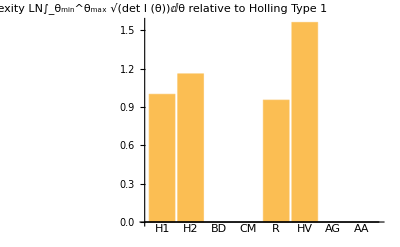

```mathematica
BarChart[NInts/NInts[[1]],ChartLabels->{"H1","H2","BD","CM","R","HV","AG","AA"},
AxesLabel->"Complexity LN∫_θ_min^θ_max √(det I (θ))ⅆθ relative to Holling Type 1"]
```

```mathematica
(*
Manipulate[
ParmRange={{a,amin,amax},{h,hmin,hmax},{γ,γmin,γmax},{m,mmin,mmax}};
NInts={
Log[NIntegrate[Sqrt[DetH1],ParmRange[[1]]]],
Log[NIntegrate[Sqrt[DetH2],ParmRange[[1]],ParmRange[[2]]]],
Log[NIntegrate[Sqrt[DetBD],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]],
Log[NIntegrate[Sqrt[DetCM],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]],
Log[NIntegrate[Sqrt[DetR],ParmRange[[1]]]],
Log[NIntegrate[Sqrt[DetHV],ParmRange[[1]],ParmRange[[4]]]],
Log[NIntegrate[Sqrt[DetAG],ParmRange[[1]],ParmRange[[2]]]],
Log[NIntegrate[Sqrt[DetAA],ParmRange[[1]],ParmRange[[2]],ParmRange[[4]]]]
};
BarChart[NInts/NInts[[1]],ChartLabels->{"H1","H2","BD","CM","R","HV","AG","AA"},
AxesLabel->"Complexity relative to Holling Type 1"]
,
{{amin,0.01},0.0001,.01},
{{amax,30},1,100},
{{hmin,0.01},0.0001,0.01},
{hmax,2,100},
{{γmin,0.01},0.0001,0.01},
{γmax,2,100},
{{mmin,0.01},0.0001,0.01},
{mmax,1,100}
]
*)
```

#### Integrate symbolically

```mathematica
IntH1=Log[Integrate[Sqrt[DetH1],a]]//FullSimplify
```

-1/2 Log[1/(75 a)]

```mathematica
IntH2=Log[Integrate[Sqrt[DetH2],a,h]]//FullSimplify
```

$Aborted

```mathematica
IntBD=Log[Integrate[Sqrt[DetBD],a,h,γ]]//FullSimplify
```

$Aborted

$Aborted

```mathematica
IntCM=Log[Integrate[Sqrt[DetCM],a,h,γ]]//FullSimplify
```

```mathematica
IntR=Log[Integrate[Sqrt[DetR],a]]//FullSimplify
```

```mathematica
IntHV=Log[Integrate[Sqrt[DetHV],a,m]]//FullSimplify
```

```mathematica
IntAG=Log[Integrate[Sqrt[DetAG],a,h]]//FullSimplify
```

```mathematica
IntAA=Log[Integrate[Sqrt[DetAA],a,h,m]]//FullSimplify
```

```mathematica
Ints={IntH1,IntH2,IntBD,IntCM,IntR,IntHV,IntAG,IntAA};
```

{-1/2 Log[1/(75 a)],IntH2,IntBD,IntCM,IntR,IntHV,IntAG,IntAA}

```mathematica
Export["Integrations_Symbolic.txt",Ints]
```

Integrations_Symbolic.txt